```mathematica
{ol500c24h,ol500c24hkeep,ol500c24hkill,ol500c24hmem,oltyp}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\ol500c24htest.mx"];
```

```mathematica
{hmp400gen,hmp800gen,hmp1400gen,hmp400keep,hmp800keep,hmp1400keep,hmp400kill,hmp800kill,hmp1400kill,hmp400mem,hmp800mem,hmp1200mem,hmp400typ,hmp800typ,hmp1400typ}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hmp500c24htest.mx"];
```

```mathematica
{hmptyp500,hmptyp600,hmptyp700,hmptyp900,hmptyp1000,hmptyp1100,hmptyp1200,hmptyp1300}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hmptyp.mx"];
```

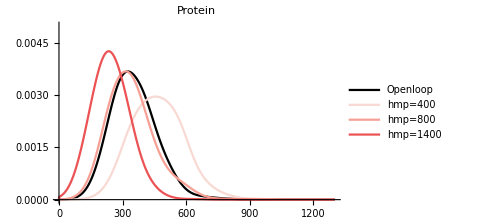

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hmp400gen[[1]][[1]]/hmp400gen[[1]][[6]],hmp800gen[[1]][[1]]/hmp800gen[[1]][[6]],hmp1400gen[[1]][[1]]/hmp1400gen[[1]][[6]]},50,PlotRange->{{0,1300},{0,0.005}},PlotLegends->{"Openloop","hmp=400","hmp=800","hmp=1400"},PlotLabel->Style["Protein",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#f8d9d3"],Thick],Directive[RGBColor["#f7a095"],Thick],Directive[RGBColor["#eb5355"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

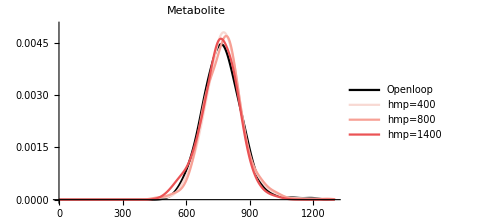

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hmp400gen[[1]][[4]]/hmp400gen[[1]][[6]],hmp800gen[[1]][[4]]/hmp800gen[[1]][[6]],hmp1400gen[[1]][[4]]/hmp1400gen[[1]][[6]]},30,PlotRange->{{0,1300},{0,0.005}},PlotLegends->{"Openloop","hmp=400","hmp=800","hmp=1400"},PlotLabel->Style["Metabolite",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#f8d9d3"],Thick],Directive[RGBColor["#f7a095"],Thick],Directive[RGBColor["#eb5355"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

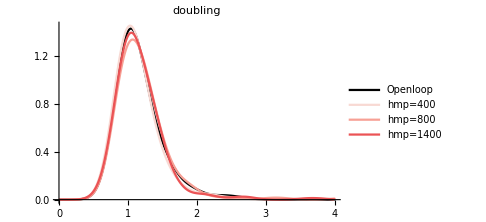

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hmp400gen[[1]][[5]],Log[2]/hmp800gen[[1]][[5]],Log[2]/hmp1400gen[[1]][[5]]},0.15,PlotRange->{{0,4},Automatic},PlotLegends->{"Openloop","hmp=400","hmp=800","hmp=1400"},PlotLabel->Style["doubling",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#f8d9d3"],Thick],Directive[RGBColor["#f7a095"],Thick],Directive[RGBColor["#eb5355"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

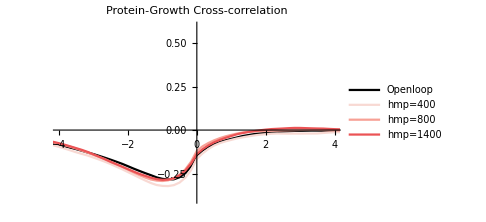

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hmp400mem[[4]],hmp800mem[[4]],hmp1200mem[[4]]},PlotRange->{{-4,4},{-0.4,0.6}},PlotLegends->{"Openloop","hmp=400","hmp=800","hmp=1400"},PlotLabel->Style["Protein-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#f8d9d3"],Thick],Directive[RGBColor["#f7a095"],Thick],Directive[RGBColor["#eb5355"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

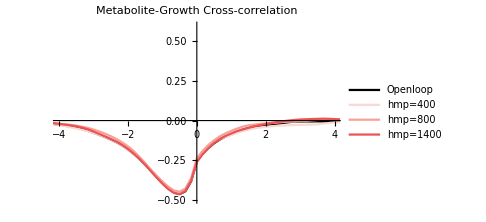

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hmp400mem[[5]],hmp800mem[[5]],hmp1200mem[[5]]},PlotRange->{{-4,4},{-0.5,0.6}},PlotLegends->{"Openloop","hmp=400","hmp=800","hmp=1400"},PlotLabel->Style["Metabolite-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#f8d9d3"],Thick],Directive[RGBColor["#f7a095"],Thick],Directive[RGBColor["#eb5355"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

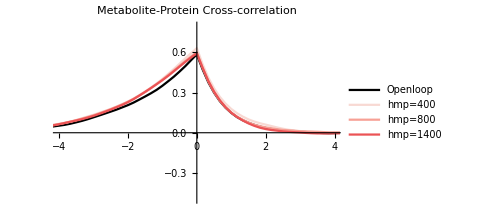

```mathematica
ListLinePlot[{ol500c24hmem[[6]],hmp400mem[[6]],hmp800mem[[6]],hmp1200mem[[6]]},PlotRange->{{-4,4},{-0.5,0.8}},PlotLegends->{"Openloop","hmp=400","hmp=800","hmp=1400"},PlotLabel->Style["Metabolite-Protein Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#f8d9d3"],Thick],Directive[RGBColor["#f7a095"],Thick],Directive[RGBColor["#eb5355"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

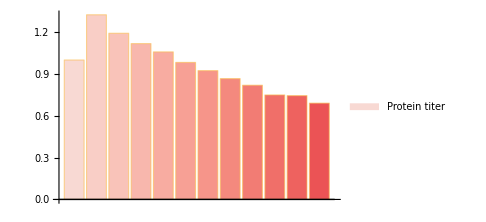

```mathematica
BarChart[{oltyp[[2]]/oltyp[[2]],hmp400typ[[2]]/oltyp[[2]],hmptyp500[[2]]/oltyp[[2]],hmptyp600[[2]]/oltyp[[2]],hmptyp700[[2]]/oltyp[[2]],hmp800typ[[2]]/oltyp[[2]],hmptyp900[[2]]/oltyp[[2]],hmptyp1000[[2]]/oltyp[[2]],hmptyp1100[[2]]/oltyp[[2]],hmptyp1200[[2]]/oltyp[[2]],hmptyp1300[[2]]/oltyp[[2]],hmp1400typ[[2]]/oltyp[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#f8d9d3"],
RGBColor["#f9cec6"],
RGBColor["#f9c3b9"],
RGBColor["#f8b7ad"],
RGBColor["#f8aca1"],
RGBColor["#f7a095"],
RGBColor["#f6958a"],
RGBColor["#f4897e"],
RGBColor["#f27c74"],
RGBColor["#f06f69"],
RGBColor["#ee625f"],
RGBColor["#eb5355"]
},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

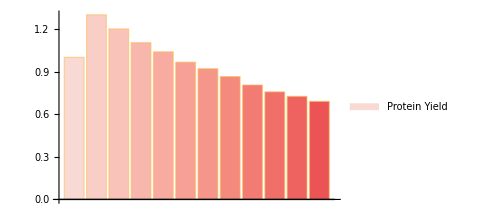

```mathematica
BarChart[{oltyp[[5]]/oltyp[[5]],hmp400typ[[5]]/oltyp[[5]],hmptyp500[[5]]/oltyp[[5]],hmptyp600[[5]]/oltyp[[5]],hmptyp700[[5]]/oltyp[[5]],hmp800typ[[5]]/oltyp[[5]],hmptyp900[[5]]/oltyp[[5]],hmptyp1000[[5]]/oltyp[[5]],hmptyp1100[[5]]/oltyp[[5]],hmptyp1200[[5]]/oltyp[[5]],hmptyp1300[[5]]/oltyp[[5]],hmp1400typ[[5]]/oltyp[[5]]},ChartLegends->{"Protein Yield"},ChartStyle->{RGBColor["#f8d9d3"],
RGBColor["#f9cec6"],
RGBColor["#f9c3b9"],
RGBColor["#f8b7ad"],
RGBColor["#f8aca1"],
RGBColor["#f7a095"],
RGBColor["#f6958a"],
RGBColor["#f4897e"],
RGBColor["#f27c74"],
RGBColor["#f06f69"],
RGBColor["#ee625f"],
RGBColor["#eb5355"]
},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

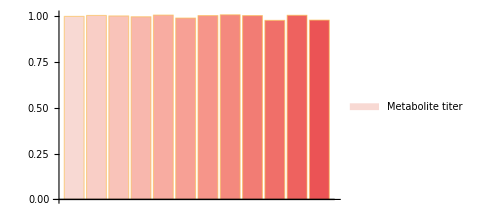

```mathematica
BarChart[{oltyp[[4]]/oltyp[[4]],hmp400typ[[4]]/oltyp[[4]],hmptyp500[[4]]/oltyp[[4]],hmptyp600[[4]]/oltyp[[4]],hmptyp700[[4]]/oltyp[[4]],hmp800typ[[4]]/oltyp[[4]],hmptyp900[[4]]/oltyp[[4]],hmptyp1000[[4]]/oltyp[[4]],hmptyp1100[[4]]/oltyp[[4]],hmptyp1200[[4]]/oltyp[[4]],hmptyp1300[[4]]/oltyp[[4]],hmp1400typ[[4]]/oltyp[[4]]},ChartLegends->{"Metabolite titer"},ChartStyle->{RGBColor["#f8d9d3"],
RGBColor["#f9cec6"],
RGBColor["#f9c3b9"],
RGBColor["#f8b7ad"],
RGBColor["#f8aca1"],
RGBColor["#f7a095"],
RGBColor["#f6958a"],
RGBColor["#f4897e"],
RGBColor["#f27c74"],
RGBColor["#f06f69"],
RGBColor["#ee625f"],
RGBColor["#eb5355"]
},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

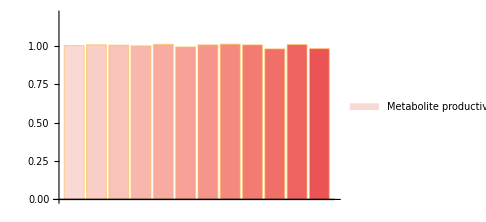

```mathematica
BarChart[{oltyp[[9]]/oltyp[[9]],hmp400typ[[9]]/oltyp[[9]],hmptyp500[[9]]/oltyp[[9]],hmptyp600[[9]]/oltyp[[9]],hmptyp700[[9]]/oltyp[[9]],hmp800typ[[9]]/oltyp[[9]],hmptyp900[[9]]/oltyp[[9]],hmptyp1000[[9]]/oltyp[[9]],hmptyp1100[[9]]/oltyp[[9]],hmptyp1200[[9]]/oltyp[[9]],hmptyp1300[[9]]/oltyp[[9]],hmp1400typ[[9]]/oltyp[[9]]},PlotRange->{0,1.2},ChartLegends->{"Metabolite productivity"},ChartStyle->{RGBColor["#f8d9d3"],
RGBColor["#f9cec6"],
RGBColor["#f9c3b9"],
RGBColor["#f8b7ad"],
RGBColor["#f8aca1"],
RGBColor["#f7a095"],
RGBColor["#f6958a"],
RGBColor["#f4897e"],
RGBColor["#f27c74"],
RGBColor["#f06f69"],
RGBColor["#ee625f"],
RGBColor["#eb5355"]
},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
{hmpgen1,hmpgen10,hmpgen50,hmpgen90,hmpgen99,hmpkeep1,hmpkeep10,hmpkeep50,hmpkeep90,hmpkeep99,hmpmem1,hmpmem10,hmpmem50,hmpmem90,hmpmem99,hmpkill1,hmpkill10,hmpkill50,hmpkill90,hmpkill99,hmptyp1,hmptyp10,hmptyp50,hmptyp90,hmptyp99}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hmp500c24hpercent.mx"];
```

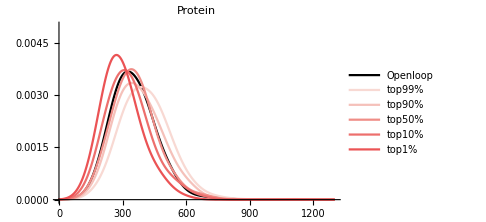

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hmpgen1[[1]][[1]]/hmpgen1[[1]][[6]],hmpgen10[[1]][[1]]/hmpgen10[[1]][[6]],hmpgen50[[1]][[1]]/hmpgen50[[1]][[6]],hmpgen90[[1]][[1]]/hmpgen90[[1]][[6]],hmpgen99[[1]][[1]]/hmpgen99[[1]][[6]]},50,PlotRange->{{0,1300},{0,0.005}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Protein",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#f8d9d3"],Thick],Directive[RGBColor["#f5c1ba"],Thick],Directive[RGBColor["#ef8d87"],Thick],Directive[RGBColor["#ed6f6d"],Thick],Directive[RGBColor["#eb5355"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

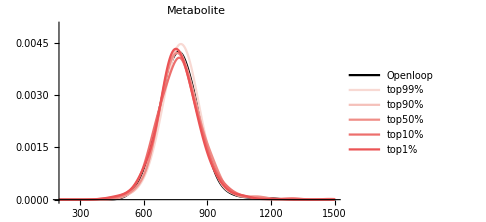

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hmpgen1[[1]][[4]]/hmpgen1[[1]][[6]],hmpgen10[[1]][[4]]/hmpgen10[[1]][[6]],hmpgen50[[1]][[4]]/hmpgen50[[1]][[6]],hmpgen90[[1]][[4]]/hmpgen90[[1]][[6]],hmpgen99[[1]][[4]]/hmpgen99[[1]][[6]]},40,PlotRange->{{200,1500},{0,0.005}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Metabolite",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#f8d9d3"],Thick],Directive[RGBColor["#f5c1ba"],Thick],Directive[RGBColor["#ef8d87"],Thick],Directive[RGBColor["#ed6f6d"],Thick],Directive[RGBColor["#eb5355"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

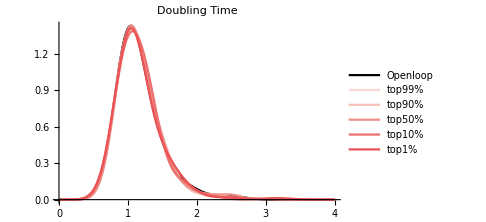

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hmpgen1[[1]][[5]],Log[2]/hmpgen10[[1]][[5]],Log[2]/hmpgen50[[1]][[5]],Log[2]/hmpgen90[[1]][[5]],Log[2]/hmpgen99[[1]][[5]]},0.15,PlotRange->{{0,4},Automatic},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Doubling Time",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#f8d9d3"],Thick],Directive[RGBColor["#f5c1ba"],Thick],Directive[RGBColor["#ef8d87"],Thick],Directive[RGBColor["#ed6f6d"],Thick],Directive[RGBColor["#eb5355"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

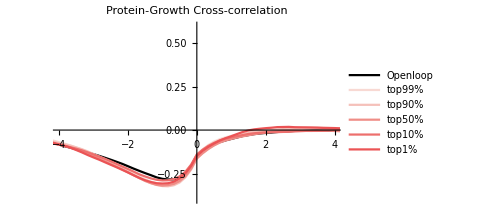

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hmpmem1[[4]],hmpmem10[[4]],hmpmem50[[4]],hmpmem90[[4]],hmpmem99[[4]]},PlotRange->{{-4,4},{-0.4,0.6}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Protein-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#f8d9d3"],Thick],Directive[RGBColor["#f5c1ba"],Thick],Directive[RGBColor["#ef8d87"],Thick],Directive[RGBColor["#ed6f6d"],Thick],Directive[RGBColor["#eb5355"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

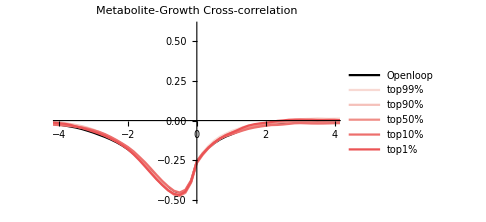

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hmpmem1[[5]],hmpmem10[[5]],hmpmem50[[5]],hmpmem90[[5]],hmpmem99[[5]]},PlotRange->{{-4,4},{-0.5,0.6}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Metabolite-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#f8d9d3"],Thick],Directive[RGBColor["#f5c1ba"],Thick],Directive[RGBColor["#ef8d87"],Thick],Directive[RGBColor["#ed6f6d"],Thick],Directive[RGBColor["#eb5355"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

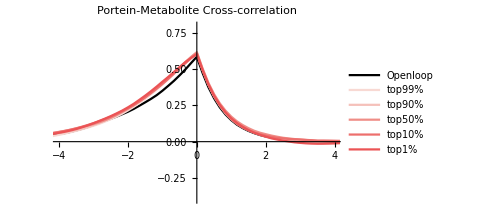

```mathematica
ListLinePlot[{ol500c24hmem[[6]],hmpmem1[[6]],hmpmem10[[6]],hmpmem50[[6]],hmpmem90[[6]],hmpmem99[[6]]},PlotRange->{{-4,4},{-0.4,0.8}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Portein-Metabolite Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#f8d9d3"],Thick],Directive[RGBColor["#f5c1ba"],Thick],Directive[RGBColor["#ef8d87"],Thick],Directive[RGBColor["#ed6f6d"],Thick],Directive[RGBColor["#eb5355"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

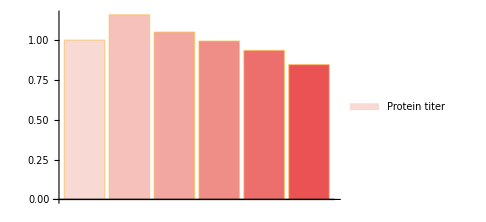

```mathematica
BarChart[{oltyp[[2]]/oltyp[[2]],hmptyp1[[2]]/oltyp[[2]],hmptyp10[[2]]/oltyp[[2]],hmptyp50[[2]]/oltyp[[2]],hmptyp90[[2]]/oltyp[[2]],hmptyp99[[2]]/oltyp[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#f8d9d3"],
RGBColor["#f5c1ba"],
RGBColor["#f2a8a1"],
RGBColor["#ef8d87"],
RGBColor["#ed6f6d"],
RGBColor["#eb5254"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

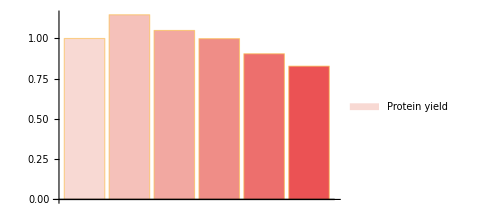

```mathematica
BarChart[{oltyp[[5]]/oltyp[[5]],hmptyp1[[5]]/oltyp[[5]],hmptyp10[[5]]/oltyp[[5]],hmptyp50[[5]]/oltyp[[5]],hmptyp90[[5]]/oltyp[[5]],hmptyp99[[5]]/oltyp[[5]]},ChartLegends->{"Protein yield"},ChartStyle->{RGBColor["#f8d9d3"],
RGBColor["#f5c1ba"],
RGBColor["#f2a8a1"],
RGBColor["#ef8d87"],
RGBColor["#ed6f6d"],
RGBColor["#eb5254"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

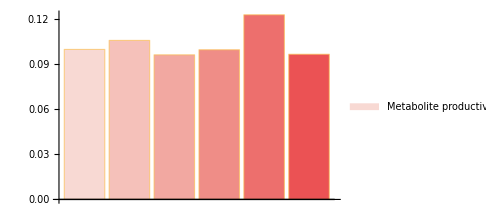

```mathematica
BarChart[{oltyp[[9]]/oltyp[[9]]-0.9,hmptyp1[[9]]/oltyp[[9]]-0.9,hmptyp10[[9]]/oltyp[[9]]-0.9,hmptyp50[[9]]/oltyp[[9]]-0.9,hmptyp90[[9]]/oltyp[[9]]-0.9,hmptyp99[[9]]/oltyp[[9]]-0.9},ChartLegends->{"Metabolite productivity"},ChartStyle->{RGBColor["#f8d9d3"],
RGBColor["#f5c1ba"],
RGBColor["#f2a8a1"],
RGBColor["#ef8d87"],
RGBColor["#ed6f6d"],
RGBColor["#eb5254"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
ListLinePlot[{oltyp[[1]],hmptyp1[[1]],hmptyp10[[1]],hmptyp50[[1]],hmptyp90[[1]],hmptyp99[[1]]},PlotLabel->"Protein titer",PlotStyle->{Black,
RGBColor["#f5c1ba"],
RGBColor["#f2a8a1"],
RGBColor["#ef8d87"],
RGBColor["#ed6f6d"],
RGBColor["#eb5254"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

-Graphics-

```mathematica
ListLinePlot[{oltyp[[3]],hmptyp1[[3]],hmptyp10[[3]],hmptyp50[[3]],hmptyp90[[3]],hmptyp99[[3]]},PlotLabel->"metabolite titer",PlotStyle->{Black,
RGBColor["#f5c1ba"],
RGBColor["#f2a8a1"],
RGBColor["#ef8d87"],
RGBColor["#ed6f6d"],
RGBColor["#eb5254"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

-Graphics-